### 2. A Partial Introduction to Localization and Fourier Analysis

Consider a particle somewhere in a one-dimensional box of length L. We’ll have the x coordinate describing the box run from -L/2 to L/2. Later I will set L=4 for definiteness.

To illustrate localization, we would like to construct a wave function out of sines and cosines that localize the particle within the region x=-L/8 to x=L/8. If the particle is going to be evenly-likely found within this range, which is L/4 long, one way to do that is to have its amplitude be the constant√(4/L) within this range, and zero elsewhere.

Because I have chosen a localization that is symmetrical about the origin, it turns out we don’t need sines and cosines. We only need the cosines because they are symmetric (even) whereas the sines are antisymmetric (odd).

Some general considerations based on boundary conditions are that the only cosines we have to consider are √(2/L)cos (n π x)/L where n is any odd integer. The square root, √(2/L), out front is put there so that the average of the function-squared is 1/L. If that function were used all by itself as a probability amplitude in the box of length L, and we then squared it to get a probability function, then the probability to find the particle somewhere in the box would be 1.

There is powerful mathematics from the world of Fourier analysis, which you definitely are not meant to understand at the moment, but which I can use to compute the appropriate combination of cosines. I will now apply the procedure, which involves integration, and I am only going to do it for n=1, 3, 5, ... ,15. If you want to go past n=15 (it is an infinite series) feel free to go further.

Since we are only doing n odd, n=15 is actually just the first 8 cosines in the series.

```mathematica
L=4;
c[x_,n_]:=Sqrt[2/L]Cos[(n Pi x)/L];
tableOfCoefficients=Table[Integrate[Sqrt[4/L]c[x,n], {x, -L/8,L/8}],{n,1,15,2}]
```

{(4 √2 Sin[π/8])/π,(2 Csc[π/8])/(3 π),(2 Csc[π/8])/(5 π),(4 √2 Sin[π/8])/(7 π),-(4 √2 Sin[π/8])/(9 π),-(2 Csc[π/8])/(11 π),-(2 Csc[π/8])/(13 π),-(4 √2 Sin[π/8])/(15 π)}

Perhaps it is nice, and maybe even more convenient to see what these coefficients are numerically:

```mathematica
N[tableOfCoefficients]
```

{0.689072,0.554523,0.332714,0.0984389,-0.0765636,-0.151233,-0.127967,-0.0459382}

#### Assembling the Series — First and Second Non-Zero Terms

First term only:

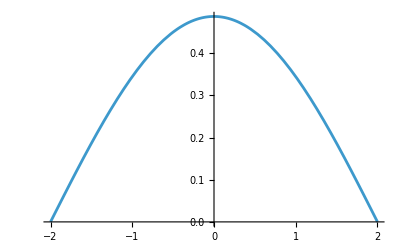

```mathematica
Plot[tableOfCoefficients[[1]]c[x,1], {x,-2, 2}]
```

Note that coefficient 2 multiplies the cosine with n=3, coefficient 3 multiplies the cosine with n=5, etc.

Here is the localized function being built up two terms:

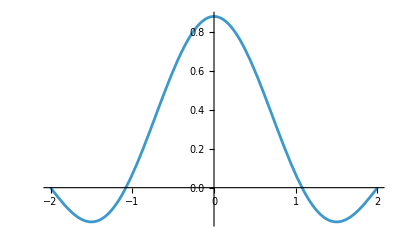

```mathematica
Plot[tableOfCoefficients[[1]]c[x,1]+tableOfCoefficients[[2]]c[x,3], {x,-2, 2}]
```

#### FOR YOU — Find some graphing program and do another term or two in the series — graph both the function and its square. The numerical values of the table of coefficients might be easier to use than the exact ones. Also, note that I have chosen L=4 so your graphs will go from -2 to 2.

#### Assembling the Series — Third and Fourth Non-Zero Terms

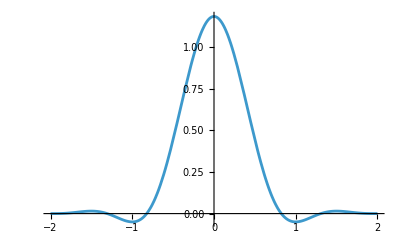

```mathematica
f4[x_]:=tableOfCoefficients[[1]]c[x,1]+tableOfCoefficients[[2]]c[x,3] + tableOfCoefficients[[3]] c[x,5]+tableOfCoefficients[[4]] c[x,7]

Plot[f4[x], {x,-2, 2}]
```

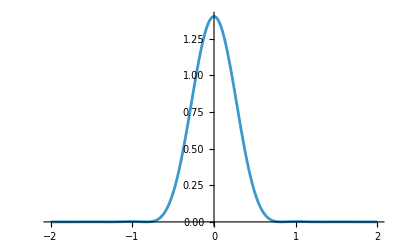

```mathematica
Plot[(f4[x])^2, {x,-2, 2}]
```

#### Assembling the Series — Eight Non-Zero Terms

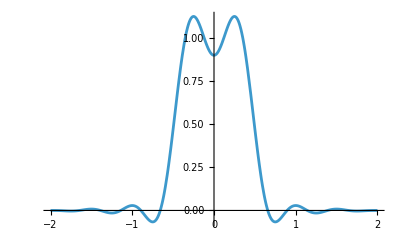

```mathematica
f8[x_]:=Sum[tableOfCoefficients[[i]]c[x,2i-1], {i, 1, 8}]

Plot[f8[x], {x,-2, 2}]
```

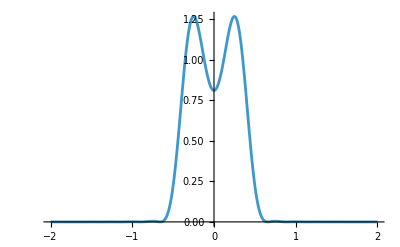

```mathematica
Plot[f8[x]^2, {x,-2, 2}]
```